{{10000,10010,10010_2,10100},{01100},{01101,10110}}

Regra 10000

(8.00497 (|ρ_1-ρ_c|)^0.975128  = ρ_u^1(T) | (ρ_1 > ρ_c))

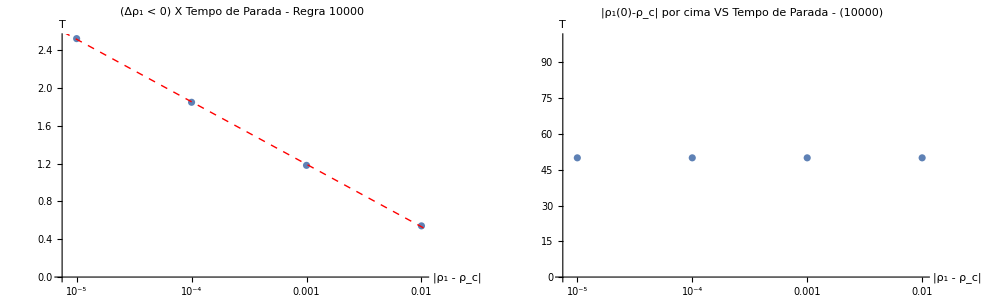

-0.789557 - 0.286935 Log[|ρ  - ρ |]
                           1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 8.00497 | 0.0603057 | 132.74 | 0.0000567493
β | 0.975128 | 0.00162436 | 600.315 | 2.77485×10^-6

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.286935 | 0.00236926 | -121.108 | 0.0000681731
τ | -0.789557 | 0.0200445 | -39.3903 | 0.000643876

Regra 10010

(9.8547 (|ρ_1-ρ_c|)^0.968501  = ρ_u^1(T) | (ρ_1 > ρ_c))

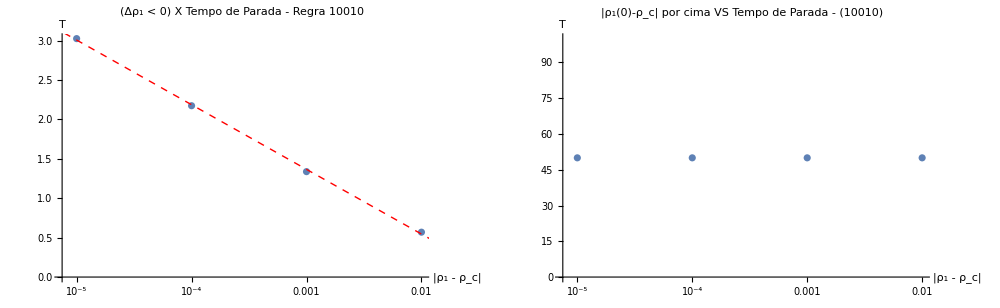

-1.09462 - 0.356199 Log[|ρ  - ρ |]
                          1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 9.8547 | 0.0643141 | 153.228 | 0.000042589
β | 0.968501 | 0.00140686 | 688.414 | 2.11008×10^-6

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.356199 | 0.00594791 | -59.8863 | 0.000278717
τ | -1.09462 | 0.0503208 | -21.7529 | 0.00210664

Regra 10010_2

(9.85478 (|ρ_1-ρ_c|)^0.968502  = ρ_u^1(T) | (ρ_1 > ρ_c))

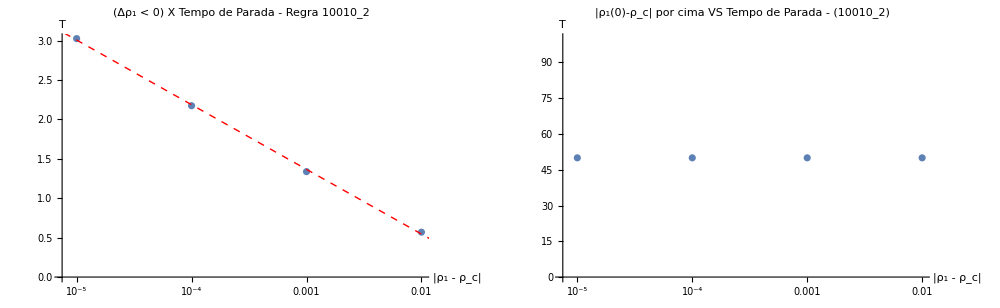

-1.09452 - 0.356181 Log[|ρ  - ρ |]
                          1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 9.85478 | 0.064343 | 153.16 | 0.0000426266
β | 0.968502 | 0.00140748 | 688.111 | 2.11194×10^-6

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.356181 | 0.00594124 | -59.9507 | 0.000278119
τ | -1.09452 | 0.0502643 | -21.7752 | 0.00210234

Regra 10100

(8.83636 (|ρ_1-ρ_c|)^0.935709  = ρ_u^1(T) | (ρ_1 > ρ_c))

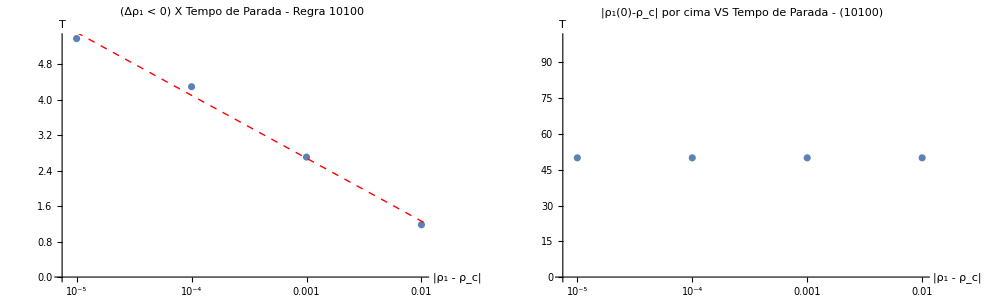

-1.57313 - 0.615252 Log[|ρ  - ρ |]
                          1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 8.83636 | 0.382205 | 23.1195 | 0.00186564
β | 0.935709 | 0.00931298 | 100.474 | 0.0000990448

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.615252 | 0.0348265 | -17.6662 | 0.00318885
τ | -1.57313 | 0.294641 | -5.33915 | 0.0333356

Regra 01100

(2.15331 (|ρ_1-ρ_c|)^1.01726  = ρ_u^1(T) | (ρ_1 > ρ_c))

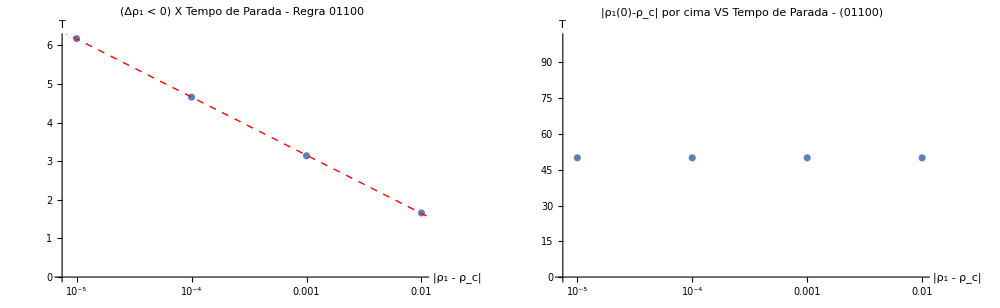

-1.36209 - 0.653815 Log[|ρ  - ρ |]
                          1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 2.15331 | 0.0190975 | 112.753 | 0.0000786483
β | 1.01726 | 0.00191469 | 531.29 | 3.5427×10^-6

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.653815 | 0.00270661 | -241.562 | 0.0000171369
τ | -1.36209 | 0.0228986 | -59.4835 | 0.000282503

Regra 01101

(1.11168 (|ρ_1-ρ_c|)^1.00824  = ρ_u^1(T) | (ρ_1 > ρ_c))

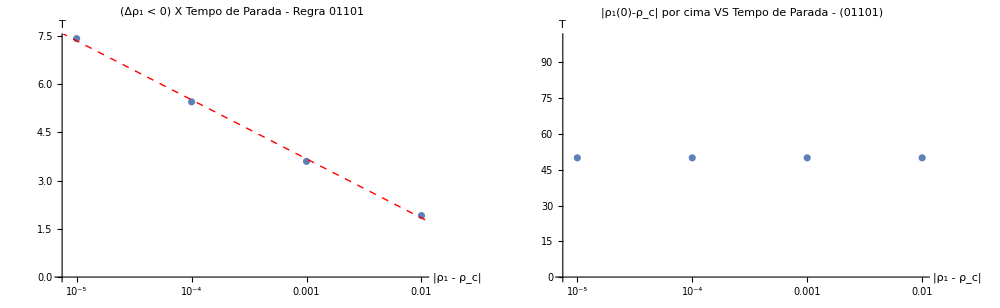

-1.83383 - 0.797548 Log[|ρ  - ρ |]
                          1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 1.11168 | 0.00577681 | 192.438 | 0.0000270024
β | 1.00824 | 0.00112158 | 898.948 | 1.23746×10^-6

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.797548 | 0.0193031 | -41.3171 | 0.000585273
τ | -1.83383 | 0.163309 | -11.2292 | 0.00783742

Regra 10110

(3.54788 (|ρ_1-ρ_c|)^0.909036  = ρ_u^1(T) | (ρ_1 > ρ_c))

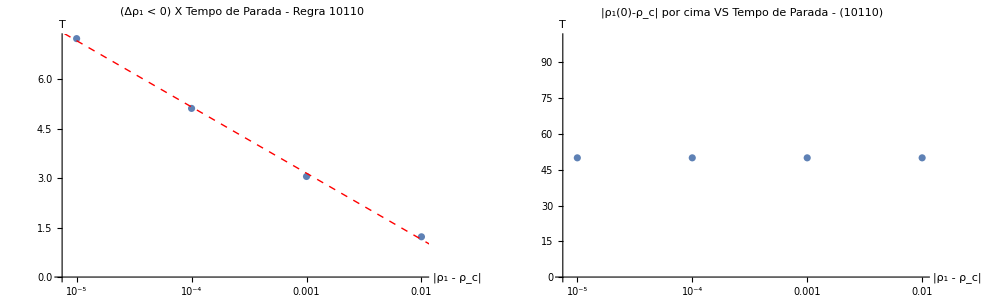

-2.8833 - 0.873949 Log[|ρ  - ρ |]
                         1    c= T | (ρ_1 < ρ_c)

| Estimate | Standard Error | t-Statistic | P-Value
k | 3.54788 | 0.10174 | 34.8721 | 0.000821311
β | 0.909036 | 0.00616737 | 147.394 | 0.0000460266

| Estimate | Standard Error | t-Statistic | P-Value
ω | -0.873949 | 0.0205677 | -42.4914 | 0.000553397
τ | -2.8833 | 0.174007 | -16.57 | 0.00362236

plot1plot2

```mathematica
tipos = {"binomiais","blinkers", "mixeds"};
prange = {"0.0001", "1e-05","1e-06","1e-07"};
lbl = {"1e-04","1e-05","1e-06","1e-07","-1e-07","-1e-06","-1e-05",  "-1e-04"};
regras = {{ "10000","10010","10010_2",  "10100"},{ "01100"},{ "01101", "10110"}}

Do[
Do[
Print[Style["Regra "<>ToString[regras[[i]][[j]]], "Section"]];
datamais=Import["/home/vynie/Documents/PycharmProjects/gameoflife/Output/ScriptOutput_TransitionRules/desvios/"<>tipos[[i]]<>"/"<>ToString[regras[[i]][[j]]]<>"/mais/ppcx.csv", HeaderLines->1];
datamenos = Import["/home/vynie/Documents/PycharmProjects/gameoflife/Output/ScriptOutput_TransitionRules/desvios/"<>tipos[[i]]<>"/"<>ToString[regras[[i]][[j]]]<>"/menos/ppcx.csv", HeaderLines->1];
datapumenos = {};
datapumais = {};
Do[
AppendTo[datapumenos, Import["/home/vynie/Documents/PycharmProjects/gameoflife/Output/ScriptOutput_TransitionRules/desvios/"<>tipos[[i]]<>"/"<>ToString[regras[[i]][[j]]]<>"/menos/"<>prange[[k]]<>"/s1.csv"][[All, {1,2}]]];
AppendTo[datapumais,Import["/home/vynie/Documents/PycharmProjects/gameoflife/Output/ScriptOutput_TransitionRules/desvios/"<>tipos[[i]]<>"/"<>ToString[regras[[i]][[j]]]<>"/mais/"<>prange[[k]]<>"/s1.csv"][[All, {1,2}]]],
{k, 1, Length[prange]-1}];
(*-------------------------------------------------------------------Plots ρu x t ------------------------------------------------------------------------*)

plots1 = ListLogLogPlot[Join[datapumais, Reverse[datapumenos]],PlotLegends->Placed[{"0.0001","1e-05","1e-06","-1e-06","-1e-05",  "-0.0001"},{Right,Top}] ,PlotLabel->"ρ_u^1 X t - Regra 10000", AxesLabel->{"t", "ρ_u^1"}, PlotRange->{{1, 10}, Automatic}, ImageSize->700, LabelStyle->{FontSize->16,FontFamily->"Arial"}, GridLines->Automatic];
If[j==1&i==1, Export["/home/vynie/Pictures/10000_pu.jpg", plots1]];
(*-------------------------------------------------------------------Plots ρu1 final------------------------------------------------------------------------*)

plotsmais =ListLogLogPlot[datamais[[All,{1, 3}]], AxesLabel->{"|ρ_1- ρ_c|", "ρ_u^1 final"},  PlotLabel->"(Δρ_1 > 0)  X  ρ_u^1 Final - Regra "<>regras[[i]][[j]]];
plotsmenos = ListLogLogPlot[datamenos[[All,{1, 3}]], AxesLabel->{"|ρ_1- ρ_c|", "ρ_u^1 final"},  PlotLabel->"(Δρ_1 < 0)  X  ρ_u^1 Final - Regra "<>regras[[i]][[j]]];
ajuste1 = NonlinearModelFit[Select[datamais[[All,{1, 3}]], #[[1]] >10^-6&], k*x^β, {k,β}, x];
plotajuste=LogLogPlot[ajuste1[x], {x, 10^-6, 1}, PlotStyle->{Red, Dashed, Thin}];


Export["/home/vynie/Pictures/puxdp_"<>ToString[regras[[i,j]]]<>".jpg",Show[plotsmais, plotajuste,Frame->All,GridLines->Automatic, ImageMargins->0,Spacings->{1,1},ImageSize->700, LabelStyle->{FontSize->18,FontFamily->"Aria"}]];
Print["\t\t\t\t\t\t\t\t\t\t\t\t\t\t\t\t\t\t"Style[" = ρ_u^1(T) | (ρ_1 > ρ_c)"k*"|ρ_1-ρ_c|"^β /. ajuste1["BestFitParameters"],Red]];

plotsmais = ListLogLinearPlot[Select[datamais[[All,{1, 2}]], #[[1]] >10^-6& ], AxesLabel->{"|ρ_1 - ρ_c|", "T"}, PlotLabel->"|ρ_1(0)-ρ_c| por cima VS Tempo de Parada - ("<>regras[[i]][[j]]<>")", PlotRange->{0, 100}];
plotsmenos= ListLogLinearPlot[Select[datamenos[[All,{1, 2}]], #[[1]] >10^-6& ], AxesLabel->{"|ρ_1 - ρ_c|", "T"},  PlotLabel->"(Δρ_1 < 0) X Tempo de Parada - Regra "<>regras[[i]][[j]]];
ajuste2 = NonlinearModelFit[Select[datamenos[[All,{1, 2}]],#[[1]] >10^-6& ], ω*Log[x]+τ, {ω,τ}, x];
plotajuste=LogLinearPlot[ajuste2[x], {x, 10^-8, 1}, PlotStyle->{Red, Dashed, Thin}];

Export["/home/vynie/Pictures/Txdp_"<>ToString[regras[[i,j]]]<>".jpg",Show[plotsmenos, plotajuste,Frame->All,GridLines->Automatic, ImageMargins->0,Spacings->{1,1},ImageSize->700, LabelStyle->{FontSize->18,FontFamily->"Aria"}]];
Print[GraphicsGrid[{{Show[plotsmenos, plotajuste], plotsmais}},Frame->All, ImageMargins->0,Spacings->{1,1},ImageSize->1000]];
Print["\t\t\t"Style[ ToString[ω*Log["|ρ_1 - ρ_c|"]+τ /. ajuste2["BestFitParameters"]]<>"= T | (ρ_1 < ρ_c)",Red]];

Print[ajuste1["ParameterTable"]];
Print[ajuste2["ParameterTable"]]

,{j, 1, Length[regras[[i]]]}],{i, 1,3} ]

Print[plot1,plot2]
```